```mathematica
ψ1[x_,t_, a_]:= a Sin[5π/2 x] Sin[0.1 5π/2 t]
```

```mathematica
ψ2[x_,t_, b_]:= b Cos[5π/2 x] Cos[0.1 5π/2 t]
```

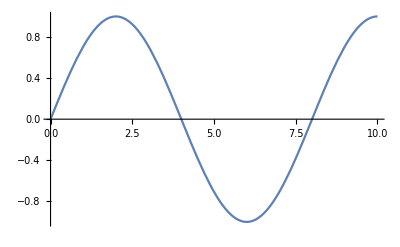

```mathematica
Plot[ψ1[1,t, 1],{t,0,10}, PlotRange->{-1,1}]
```

```mathematica
Animate[Plot[ψ1[x,t, 1],{x,0,1}, PlotRange->{-1,1}],{t,0,10}]
```

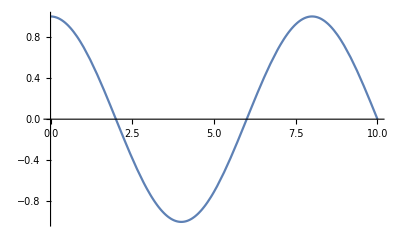

```mathematica
Plot[ψ2[0,t, 1],{t,0,10}, PlotRange->{-1,1}]
```

```mathematica
Animate[Plot[ψ2[x,t, 1],{x,0,1}, PlotRange->{-1,1}],{t,0,10}]
```

```mathematica
Animate[Plot[ψ1[x,t, 1]+ψ2[x,t, 1],{x,0,1}, PlotRange->{-1,1}],{t,0,10}]
```

```mathematica
Animate[Plot[ψ1[x,t, 1]-ψ2[x,t, 1],{x,0,1}, PlotRange->{-1,1}],{t,0,10}]
```

```mathematica
ψ1[x,t, 1]
```

Sin[0.785398 t] Sin[(5 π x)/2]

```mathematica
Manipulate[Animate[Plot[ψ1[x,t, 1]+ψ1[x+2/(5)α,t+10*2/(5)β, 1],{x,0,1}, PlotRange->{-3,3}],{t,0,10}],{α,-1,1},{β,-1,1}]
```